# Empirical P vs. NP: When Different Turing Machines Compute the Same Function

Michael Sun

Wolfram High School Summer Research Program 2025

A Turing machine is a theoretical model of computation classified as an automaton invented by Alan Turing that operates on an infinite tape of sequential memory. The significance of Turing machines, as described in the Church-Turing thesis, comes from their ability to compute any function and therefore have the same computational ability as all conventional computers. Empirical evidence suggests that there exists Turing machines that follow different rules but ultimately compute the same function, presumably for all inputs. Naturally, these machines will have different runtimes, which models multiple computers running different algorithms to reach the same goal. Similarly, motivation for studying complexity theory comes from analyzing and improving algorithms. A central unsolved problem in the field is if quickly verifying a solution to a problem implies the existence of an algorithm that quickly solves it—commonly known as the P vs. NP problem. Analyzing patterns in the range of runtimes for equivalent Turing machines provides potential for empirically guessing at whether P equals NP.

## Introduction

Turing machines can be formally defined as a tuple of a set of states, a halt state, a set of symbols called its alphabet, and a lookup table of all possible state-symbol pairs. Turing machines keep a pointer to the cell it is currently reading, and the symbol on this cell combined with its current state defines a transition. For each transition, three operations occur: read the symbol on the current cell, write a (not necessarily distinct) symbol to the current cell, and move to an adjacent cell. Certain traits of a Turing machine are unfortunately difficult to quickly represent with a computer, so the results in this essay will be close approximations of the real behavior of Turing machines. Specifically, we will bound a finite section of the tape and set a halting condition not dependent on its state for convenience. Additionally, we will focus on 2-symbol Turing machines since any machine can be reduced to a 2-symbol Turing machine.

### Terminology

Here, the variables  and  generally refer to the  states and  symbols of a Turing machine. Additionally, I define setting a Turing machine to a nonnegative integer  as filling our chosen interval  of the tape of length  for some  with the binary representation of  in big endian (natural left-to-right order). We ensure that  (i.e. the number of bits fits in ). Additionally, I define the value of a Turing machine as the number created by each cell on  as base- digits.

### Formalism

Let  be the set of all -state -color Turing machines. Each machine in  represents a partial function  with input specified by the base  number formed by the closed interval  on the tape, where each symbol is an integer between 0 and . Define two Turing machines in  to be equivalent if they compute the same partial function on , or both do not exist. The number of distinct machines is the cardinality of . For each equivalence class, we will analyze patterns of the worst-case running times of each machine in the class and over all classes in  for different  and .

Evolution of the partial (and total) function  described by rule 451 for  and input :

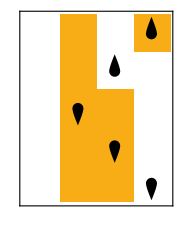

```mathematica
RulePlot[TuringMachine[445],{{1,4},{IntegerDigits[5,2,4],0}},4,ImageSize->Small]
```

## Theory

Due to the universality of Turing machines from the Church-Turing thesis, this fundamental and mathematical model of computation reveals results about computability and logical (un)decidability. A problem is undecidable if and only if it is provable that there exists no algorithm that will always return the correct answer to the problem. Turing’s major result was his proof of the undecidability of determining if a computer program halts, famously known as the halting problem.

### The Halting Problem and Rice’s Theorem

### Computational Complexity

## Implementation

Due to the undecidability of universal static analysis and the computational irreducibility of Turing machine evolution, the implementation will inevitably be brute-force in nature. However, there are certain ways to prune the search space by examining only the rules. There are also optimizations for Turing machine simulation, particularly with memoizing sections of the tape.

### Pruning

Despite the undecidability of finding a universal way of reducing computation across Turing machines or even on one Turing machine, we can take inspiration from DFA (deterministic finite automaton) minimization. Specifically, one big optimization we can make is to declare that all Turing machines with rules that permute a dead state (unreachable from the initial state) to be equal: each of these permutations are unreachable anyway.

The diagram below shows two equivalent Turing machines, each with a different permutation of the rules from state 2, which is unreachable from state 1.

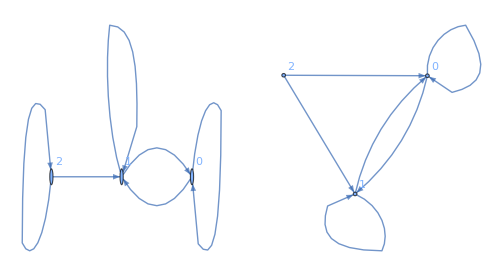

```mathematica
GraphicsRow[{
Graph[{1->1,1->0,0->1,0->0,2->1,2->2},VertexLabels->Automatic],
Graph[{1->1,1->0,0->1,0->0,2->0,2->1},VertexLabels->Automatic]
}]
```

Determining the reachable nodes reduces to graph traversal. It is not hard to see that all state graphs have  vertices and  edges, resulting in a runtime of .

The numbering system of Turing machines in the Wolfram Language permutes rules in the following order: direction (-1 to 1), symbol (0 to ), then state (1 to ). For the rest of the essay, we will use this numbering without loss of generality. Notice that for consecutive unreachable states ending in state  (e.g. 2, 3 for ), their rule numbers will also be grouped separately so we only need to define the interval (start and end) of rule numbers of an equivalence class. For example, suppose that state 3 is unreachable for . Then there exists contiguous intervals of rules that are isomorphic, such as rules 83520 to 84096. Thus, for each of these blocks, we can skip ahead to the end of a block when we encounter its beginning. Consequently, this is also the only time we can speed up iteration.

The length of an iteration depends on the number of reachable states. If there are  reachable states from 1 to , then there are  unreachable states. The number of ways we can permute these unreachable states is given by , since there are  symbols per state and  ways to permute each single component of a rule.

Set number of states and symbols:

```mathematica
states=3;
symbols=2;
machines=(2*states*symbols)^(states*symbols);
```

getinfo requires the full form of a rule, but rule numbers are easier to comprehend, so we will use the following two resource functions to convert between them.

Resource functions to convert between rule full form and rule number:

```mathematica
tmRuleFromNum=ResourceFunction["TuringMachineFromNumber"];
tmRuleToNum=ResourceFunction["TuringMachineToNumber"];
```

Gets a rule’s hash map key and generate a state diagram from the rule:

```mathematica
getinfo[r_]:={r[[All,2]],Graph[r[[All,All,1]]]}
```

The key construction will be to point all unreachable states to 1’s so that they map to the beginning of an equivalent block of rules if the condition is satisfied. The following function gets this key and the state graph of a machine.

Transforms a return value from getinfo into a hash key such that all equivalent Turing machines have the same key:

```mathematica
cftransform=
FunctionCompile[
Function[
{
Typed[states,"MachineInteger"],
Typed[reachable,"PackedArray"::["MachineInteger",1]],
Typed[key,"PackedArray"::["MachineInteger",1]]
},
Flatten@
Table[
If[
MemberQ[reachable,j],
Flatten@Table[key[[k]],{k,6*j-5,6*j}],
Table[1,6]
],
{j,states}
]
]
];
```

Returns :

```mathematica
perm[d_Integer]:=(2*states*symbols)^(symbols*(states-d))
```

Checks if l is a consecutive list that starts with 1:

```mathematica
consQ[l:{___Integer}]:=First[l]==1&&Most[l]+1===Rest[l]
consQ[_List]:=False
```

Takes in the number of rules to analyze from 0 to len-1 and loops through those rules, skipping if possible.

```mathematica
prune[len_Integer]:=
Module[{rcur,tmp,cnt=CreateDataStructure["Counter",0]},
Do[
If[
cnt["Get"]>0,
cnt["Decrement"],
With[{info=getinfo[tmRuleFromNum[i,states,symbols]]},
rcur=VertexOutComponent[info[[2]],1];
map[
"Insert",
(#->map["Lookup",#,0&]
+If[
consQ[Sort[rcur]],
tmp=perm[Length[rcur]];cnt["Set",tmp-1];tmp,
1
]
)&@cftransform[states,rcur,Flatten@info[[1]]]
];
]
],
{i,0,len-1}
]
]
```

Call the function:

```mathematica
map=CreateDataStructure["HashTable"];
prune[machines];
elems=map["Elements"];
```

Or get precomputed data from the cloud:

```mathematica
elems=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/18a0dc05-36a4-42da-b07c-fd940256d0f4"](https://www.wolframcloud.com/obj/18a0dc05-36a4-42da-b07c-fd940256d0f4)]];
```

We can confirm that equivalence classes (not just those that are consecutive) come in sizes of  for all nonnegative . In this case, for , we indeed have , , .

```mathematica
DeleteDuplicates[elems[[All,2]]]
```

{1,144,20736}

### Rule Extraction

Now we convert the rules back to their canonical numbered form for indexing during analysis and piece together information about each rule and its evolution. key stores the Turing machine rule keys, and vals stores the pruned rules, which are strung together to form a Turing machine rule.

Reconstruct full form rules:

```mathematica
fullRules=With[
{
key=Transpose@{
Riffle[Range[states],Range[states]],
Table[BitAnd[i,1],{i,states*symbols}]
},
vals=Partition[#[[1]],3]&/@elems
},
ParallelMap[Table[key[[i]]->#[[i]],{i,states*symbols}]&,vals]
];
```

Convert full form rules to numbered rules:

```mathematica
ruleNumsCompressed=Map[tmRuleToNum[#][[1]]&,fullRules];
```

Or get precomputed data from the cloud:

```mathematica
ruleNumsCompressed=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/e5e6b260-f207-4614-8856-fe336facc2cf"](https://www.wolframcloud.com/obj/e5e6b260-f207-4614-8856-fe336facc2cf)]];
```

Free memory;

```mathematica
fullRules=.
```

### Search

As mentioned, the behavior or a Turing machine is undecidable even on a finite tape, so we must find optimization in our simulation implementation. One notable bottleneck—amongst others—is repeating and non-terminating Turing machines. Optimizing repeating machines can be naturally solved by memoizing a “snapshot” of the Turing machine for each independent round of simulation of a machine and an input. After each iteration, we check if the current snapshot has been seen before. If we arrive from a snapshot back to the same snapshot, we know we have a loop and we can terminate. Further, since we test all inputs from 0 to 2^(bits-1) for the same Turing machine, we can keep a persistent collection of snapshots between inputs for each Turing machine. A snapshot of a Turing machine consists of the tuple  where  is the cell the Turing machine is currently pointing to and  is the DP radius.

The TuringMachine function likely contains internal optimizations for evolving the Turing machine for multiple states at a time, so individual iterations of NestWhile is going to be slow. However, we inherently need to iterate to avoid slowdowns with running way too many Turing machine iterations. My solution (and potentially most naive) is to iterate through blocks of Turing machines. This way, we can leverage internal optimizations while still iterating.

TODO: talk abt adding something that detects if the turing machine is going to move in one direction forever

Set the DP radius, tape width, and bits to enumerate

```mathematica
dprad=32;
width=64;
bits=5;
```

Gets the next block of evolutions of a Turing machine given the previous block:

```mathematica
stepTM[rule_Integer,stages_List,blockwidth_Integer]:=
With[
{tms=TuringMachine[{rule,states,symbols},stages[[-1]],blockwidth]},
Transpose@{
tms[[All,1]],
PadLeft[#[[2]],width,0,width-Length[#[[2]]]]&/@tms
}
]
```

I have implemented both DP tables to be least frequently used (LFU) caches for speed and reduced memory overhead. As consequence, this also means that there is an upper bound to the number of snapshots that can be stored.

Generate the halting configuration for each rule:

```mathematica
htDP[rule_Integer,bits_Integer,blockwidth_Integer,maxdepth_Integer]:=
Transpose@
With[{dpG=CreateDataStructure["LeastRecentlyUsedCache",256]},
Table[
Module[
{
dp=CreateDataStructure["LeastRecentlyUsedCache",256],
i=CreateDataStructure["Counter",1],
cnt=CreateDataStructure["Counter",0],
tms,tmp,
flag=False,
cur={{0,0,0}}
},
tms=NestWhile[
stepTM[rule,#,blockwidth]&,
stepTM[rule,{{{1,width,0},{IntegerDigits[n,2,width],0}}},blockwidth],
(
i["Set",1];
While[
cur=#[[i["Get"]]];
i["Get"]<=blockwidth&&!flag&&cur[[1,3]]<=0,

tmp=Join[
{cur[[1,1]],cur[[1,3]]},
PadLeft[cur[[2]],2*dprad-1,0,dprad+cur[[1,3]]-1]
];
If[
!(flag=dpG["KeyExistsQ",tmp]),
If[
(flag=dp["KeyExistsQ",tmp]),
dpG["Insert",tmp->1],
dp["Insert",tmp->1]
]
];
i["Increment"];
cnt["Increment"];
];
i["Get"]==blockwidth+1&&!flag&&cur[[1,3]]<=0
)&,
1,maxdepth
];
Flatten[{
If[flag||cnt["Get"]==maxdepth*blockwidth,-1,cnt["Get"]],
If[tms[[i["Get"],1,3]]==1,FromDigits[tms[[i["Get"],2]],2],-1]
}]
],
{n,1,2^bits-1}
]
]
```

```mathematica
chtDP=
Compile[
{
{rule,_Integer},
{bits,_Integer},
{blockwidth,_Integer},
{maxdepth,_Integer}
},
htDP[rule,bits,blockwidth,maxdepth],
{{htDP[___],_Integer,2}},
CompilationTarget->"C",
CompilationOptions->{"InlineExternalDefinitions" -> True},
RuntimeOptions->"Speed",
RuntimeAttributes->{Listable}
];
```

Call function in parallel. Wolfram internal parallelization functions preserve order.

```mathematica
halts=ParallelMap[chtDP[#,4,4,32]&,ruleNumsCompressed];
```

Join the computed information in the form{rule, # times repeated, {halt times}, {halt values}}

```mathematica
haltconfig=Transpose@{
ruleNumsCompressed,
elems[[All,2]],
halts[[All,1]],
halts[[All,2]]
};
```

```mathematica
halts=.
```

Groups each halting configuration in the form{{range, min, max, rules...}...}

```mathematica
haltgroups32=
Map[
With[
{ttl=Total[#[[All,2]]],mm=MinMax[Max[#[[3]]]&/@#]},
Flatten@{mm[[2]]-mm[[1]],mm,#[[All,1]]}
]&,
GatherBy[
Select[haltconfig,!ContainsOnly[#[[3]],{-1}]&],
#[[4]]&
]
];
```

## Distribution Analysis

```mathematica
genplot[data_List]:=
With[
{
sup=Length@data,
sizsup=Max[Length/@data]-3,
step=IntegerPart[Length@data/400],
sizstep=IntegerPart[Max[Length/@data]/400]
},
Manipulate[
With[{
w=1000,
sorted=SortBy[
data,Switch[
sort,
"Runtime Range",-First[#]&,
"Class Size",-Length[#]&,
"Max Runtime",-#[[3]]&,
"Min Runtime",-#[[2]]&
]
]
},
Column[{
ListPlot[
((Length/@sorted)-3)[[Min[a,b];;b]],
Joined->True,
PlotRange->{{Automatic,Automatic},{Automatic,sizbound}},
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Equivalence Class Size",
PerformanceGoal->"Speed"
],
ListPlot[
(First/@sorted)[[Min[a,b];;b]],
Joined->True,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/10,
PlotLabel->"Runtime Range",
PerformanceGoal->"Speed"
],
ListPlot[
{sorted[[All,2]][[Min[a,b];;b]],sorted[[All,3]][[Min[a,b];;b]]},
Joined->True,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/6,
PlotLabel->"Maximum and Minimum Runtime",
PlotLegends->{"Min","Max"},
PerformanceGoal->"Speed"
]
}]
],
{{a,1,"Left bound"},1,sup,step,Appearance->"Labeled"},
{{b,sup,"Right bound"},1,sup,step,Appearance->"Labeled"},
{{sort,"Runtime Range","Sort by"},{"Runtime Range","Class Size","Max Runtime","Min Runtime"}},
{{sizbound,sizsup,"Size upper bound"},50,sizsup,sizstep,Appearance->"Labeled"},
SaveDefinitions->True
]
]
```

Get precomputed (3,2) data from the cloud:

```mathematica
haltgroups32=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/cd09d92f-87f5-45cc-b958-f117a03cef75"](https://www.wolframcloud.com/obj/cd09d92f-87f5-45cc-b958-f117a03cef75)]];
```

```mathematica
genplot[haltgroups32]
```

```mathematica
stackPoints[l_List]:=MapIndexed[Function[{value,index},{First@index,#}&/@value]]@l
Rasterize[
With[{w=1600},
ListPlot[
stackPoints[SortBy[haltgroups32,-First[#]&][[;;256,4;;]]],
PlotRange->Full,
ImageSize->{w,Automatic},
AspectRatio->1/3,
PlotLabel->"Distribution of the First 256 Turing Machine Rules, Sorted by Runtime Range",
PlotHighlighting->None
]
]
]
```

-Graphics-

TODO: plot runtime graphs

```mathematica
haltgroups23=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/fcc296dd-6d0b-4345-b5e7-1694ad35d0cd"](https://www.wolframcloud.com/obj/fcc296dd-6d0b-4345-b5e7-1694ad35d0cd)]];
```

```mathematica
genplot[haltgroups23]
```

The graphs for 3-state 2-symbol and 2-symbol 3-state machines look almost identical, but are not the same.

Number of equivalence classes that differ between (2,3) and (3,2) Turing machines:

```mathematica
Length@Complement[haltgroups32,haltgroups23]
```

412

```mathematica
sorted22=SortBy[haltgroups22,-First[#]&];
```

### Runtime Analysis

```mathematica
genRuntimePlot[index_Integer,nstates_Integer,nsymbols_Integer,bits_Integer]:=
Block[{states=nstates,symbols=nsymbols},
With[{data=DeleteDuplicates[chtDP[sorted22[[index,4;;]],bits,8,64]]},
Manipulate[
Show[
Plot[dy,{x,1,2^bits},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[loga*Log2[x]+dy,{x,1,2^bits},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[lina*x+dy,{x,1,2^bits},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[qa*x^2+dy,{x,1,2^bits},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[ea*2^x+dy,{x,1,2^bits},PlotStyle->{Dashed,Thickness[0.0025]}],
ListPlot[
data[[All,1]],
DataRange->{0,Length@data[[1,1]]-1},
Joined->True,
PlotRange->All,
PerformanceGoal->"Speed"
],
PlotRange->{{1,2^bits},{0,Max[data[[All,1]]]}},
AspectRatio->1/2,
ImageSize->Large
],
{{dy,0,"y shift"},0,50,Appearance->"Labeled"},
{{loga,1,"Logarithmic constant"},1,10,Appearance->"Labeled"},
{{lina,1,"Linear constant"},0.1,10,Appearance->"Labeled"},
{{qa,1,"Polynomial constant"},0.1,2,Appearance->"Labeled"},
{{ea,1,"Exponential constant"},0.1,2,Appearance->"Labeled"},
SaveDefinitions->True
]
]
]
```

```mathematica
genRuntimePlot[6,2,2,8]
```

## Existing Work

This approach can also be applied to different numbers of states and symbols, and agrees with Wolfram’s findings on page 761 of A New Kind of Science. He found that the set of all 2-state 2-symbol Turing machines computes exactly 351 distinct functions, which is the same number I found.

Shown below is the plot of 2-state 2-color Turing machines.

```mathematica
haltgroups22=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/8b605cb9-0b20-4efd-a2f5-fa0545cb6b10"](https://www.wolframcloud.com/obj/8b605cb9-0b20-4efd-a2f5-fa0545cb6b10)]];
```

```mathematica
genplot[haltgroups22]
```

## Conclusions

## Future Work

stream algorithm?
analyze state diagram patterns to extend beyond dfa minimzation
optimize htdp for parallel cores by sacrificing total dp?? test performance
make dp better by extrapolating directions/skip steps

## Acknowledgements

type

## References

Ariel (https://cs.stackexchange.com/users/27055/ariel), Given two total Turing machines, is it undecidable problem to detect whether they give the same output on all inputs?, URL (version: 2015-08-30): https://cs.stackexchange.com/q/45687

Manlio (https://math.stackexchange.com/users/22701/manlio), How are weakly universal Turing machines actually defined?, URL (version: 2020-04-22): https://math.stackexchange.com/q/3634837

Weisstein, Eric W. “Turing Machine.” From MathWorld--A Wolfram Resource. https://mathworld.wolfram.com/TuringMachine.html

Wikipedia contributors. (2025, June 30). Automata theory. In Wikipedia, The Free Encyclopedia. Retrieved 15:56, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Automata_theory&oldid=1298074772

Wikipedia contributors. (2025, April 14). DFA minimization. In Wikipedia, The Free Encyclopedia. Retrieved 15:59, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=DFA_minimization&oldid=1285525404

Wikipedia contributors. (2025, June 12). Halting problem. In Wikipedia, The Free Encyclopedia. Retrieved 21:23, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Halting_problem&oldid=1295203495

Wikipedia contributors. (2025, March 18). Rice’s theorem. In Wikipedia, The Free Encyclopedia. Retrieved 15:58, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Rice%27s_theorem&oldid=1281112418

Wikipedia contributors. (2025, June 24). Turing machine. In Wikipedia, The Free Encyclopedia. Retrieved July 2, 2025, from https://en.wikipedia.org/w/index.php?title=Turing_machine&oldid=1297184647

Wikipedia contributors. (2025, March 17). Universal Turing machine. In Wikipedia, The Free Encyclopedia. Retrieved 15:55, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Universal_Turing_machine&oldid=1281033475

Wolfram, S. (2002). A New Kind of Science. Retrieved from https://www.wolframscience.com